```mathematica
outputDir =FileNameJoin[{ NotebookDirectory[],"/data_genomesize100_generations1000_mut0p01_cadist10"}];
filePrefix="all_target_1_size_1_";
fileName[x_]:=FileNameJoin[{outputDir,x}];
listOfStringsToNumbers[list_]:=Map[Map[ToExpression,Characters[#]]&,list]
importGenotypes[x_]:=listOfStringsToNumbers[Import[fileName[filePrefix<>"genotypes_"<>ToString[x]<>".csv"],{"Text","Lines"}]];
importPhenotypes[x_]:=listOfStringsToNumbers[Import[fileName[filePrefix<>"phenotypes_"<>ToString[x]<>".csv"],{"Text","Lines"}]];
importFitnesses[x_]:=Import[fileName[filePrefix<>"fitnesses_"<>ToString[x]<>".csv"],"List"];
arrayPlotGrid[list_]:=
Grid[ArrayPlot[#1]&/@list];
viewGeneration[x_]:=Grid[{ArrayPlot[CellularAutomaton[110,#,{100,All}]]&/@importGenotypes[x]}];
importGenotype[i_,j_]:=importGenotypes[i]⟦j⟧;
importPhenotype[i_,j_]:=importPhenotypes[i]⟦j⟧;
importFitness[i_,j_]:=importFitnesses[i]⟦j⟧;
```

```mathematica
mappingStats[gens_,phens_,i_]:=Map[{HammingDistance[gens⟦i⟧,gens⟦#⟧],HammingDistance[phens⟦i⟧,phens⟦#⟧]}&,Range[1,Length[gens]]];
fitnessStats[gens_,fits_,i_]:= Map[{HammingDistance[gens⟦i⟧,gens⟦#⟧],Abs[fits⟦i⟧-fits⟦#⟧]}&,Range[1,Length[gens]]];;
randomSamples[i_]:=Transpose[{RandomSample[Range[100],i],RandomSample[Range[100],i]}];
randomSample[i_,j_]:=Transpose[{ConstantArray[i,j],RandomSample[Range[100],j]}];
randomGenPhenMappings[sample_(*list of generation,genotype pairs*)]:=Flatten[mappingStats[importGenotypes[#1],importPhenotypes[#1],#2]&@@@sample,1];
randomGenFitMappings[sample_(*list of generation,genotype pairs*)]:=Flatten[fitnessStats[importGenotypes[#1],importFitnesses[#1],#2]&@@@sample,1];

plotRow[x_]:=ArrayPlot[{x},Mesh->True]
pdf3D[points_]:=Plot3D[PDF[SmoothKernelDistribution[points],{x,y}],{x,0,100},{y,0,100},PlotRange->{0,MaxValue[PDF[SmoothKernelDistribution[points],{x,y}],{x,y}]}];
hist3D[points_]:=Histogram3D[points,Automatic,"PDF", ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"LightTemperatureMap"],AxesLabel->{Framed["Hamming Distance, H",Background->White],Framed["Fitness, F",Background->White],Framed["P(F|H)",Background->White]},ViewPoint->{Front,Left,Top}];(*x: hamming distance, y: fitness, z: probability *)
hist2D[points_]:=Labeled[DensityHistogram[points,Automatic,"Count",ColorFunction->"LightTemperatureMap" , AxesLabel->{"H","F"}],{corr[points],Rotate[Generation,90Degree],Genome},{Top,Left,Bottom}];
genomeHist[i_,j_]:=Labeled[hist3D[randomGenFitMappings[{{i,j}}]],plotRow[importGenotype[i,j]]];
genomeHist2D[i_,j_]:=Labeled[hist2D[randomGenFitMappings[{{i,j}}]],plotRow[importGenotype[i,j]]];
genomePlot[i_,j_]:=Labeled[ListPlot[randomGenFitMappings[{{i,j}}],DataRange->{0,100}],plotRow[importGenotype[i,j]]];

corr[points_]:=N[If[And@@Map[StandardDeviation[#]>0&,Transpose[points]],N[Correlation@@Transpose[points]],0]]
genomeCorr[i_,j_]:=corr[randomGenFitMappings[{{i,j}}]];
genomeCorrs[i0_,j0_]:=Table[genomeCorr[i,j],{i,1,i0},{j,1,j0}]
phenotypeCorr[i_,j_]:=corr[randomGenPhenMappings[{{i,j}}]];
phenotypeCorrs[i0_,j0_]:=Table[phenotypeCorr[i,j],{i,1,i0},{j,1,j0}]

corrHist[corrs_]:=Histogram[Flatten[corrs],AxesLabel->{Correlation}]
corrPlot[corrs_]:=Labeled[ArrayPlot[corrs,FrameTicks->Automatic,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic],{Rotate[Generation,90 Degree],TraditionalForm[Genome]},{Left,Top}]
corrPlot3D[corrs_]:=ListPlot3D[corrs,AxesLabel->{Genome,Generation},ColorFunction->"LightTemperatureMap"]

findMaxes[mats_, k_]:=Module[{maxRows,maxCols},
maxRows= Ordering[mats,-k];
maxCols =Map[Ordering[#,-1][[1]]&,mats[[maxRows]]];
Transpose[{maxRows,maxCols}]
]
findMaxesFlat[mats_,i_,k_]:=Module[{list,maxCols},
list=mats[[i]];
maxCols=Ordering[list,-k];
Map[Join[{i},{#}]&,maxCols]
]
```

```mathematica
findMaxesFlat[{1,5,7,4},2]
```

{{1,2},{1,3}}

```mathematica
Ordering[{1,5,7,4},-2]
```

```mathematica
Map[Join[{#},{4,5,6}]&,{2,3}]
```

{{2,4,5,6},{3,4,5,6}}

```mathematica
genomeComparison[i_,j_]:=Module[{gens,points,dists,fits},
gens=importGenotypes[1];
points=randomGenFitMappings[{{1,1}}];
dists=Transpose[points][[1]];
fits=Transpose[points][[2]];
Grid[{{
ArrayPlot[gens[[All,1;;80]],Frame->True,PlotRangePadding->0],
ArrayPlot[Transpose[{dists}],PlotRangePadding->0],
ArrayPlot[Transpose[{fits}],PlotRangePadding->0]
}},ItemSize->{Automatic,40}]
]
```

```mathematica
pcorrs=phenotypeCorrs[100,50];
Export[fileName["pcorrs.csv"],corrs,"Table"]
```

/Users/caseygrun/codeshare/cs289/cs289-final-project/data_genomesize100_generations1000_mut0p01_cadist10/pcorrs.csv

```mathematica
pcorrs
```

```mathematica
corrHist[pcorrs]
corrPlot[pcorrs]
```

```mathematica
corrs=genomeCorrs[100,50];
Export[fileName["corrs.csv"],corrs,"Table"]
```

/Users/caseygrun/codeshare/cs289/cs289-final-project/data_genomesize100_generations1000_mut0p01_cadist10/corrs.csv

```mathematica
corrs=Import[fileName["corrs.csv"],"Table"];
```

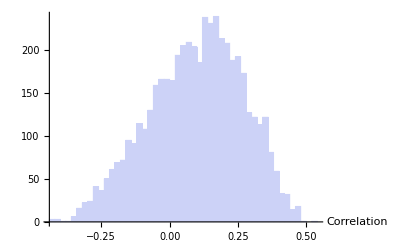

```mathematica
corrHist[corrs]
corrPlot[corrs]
```

```mathematica
Export[fileName["corrs-plot.pdf"],-Graphics-GenerationGenome]
```

/Users/caseygrun/codeshare/cs289/cs289-final-project/data_genomesize100_generations1000_mut0p01_cadist10/corrs-plot.pdf

```mathematica
Export[fileName["corrs-dist.pdf"],-Graphics-]
```

/Users/caseygrun/codeshare/cs289/cs289-final-project/data_genomesize100_generations1000_mut0p01_cadist10/corrs-dist.pdf

```mathematica
Grid[Table[genomePlot[i,j],{i,75,75},{j,1,10}]]
```

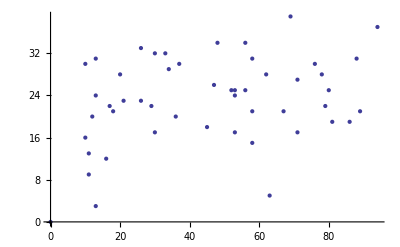
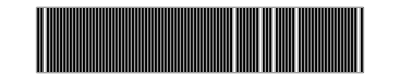
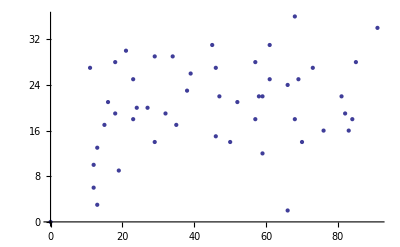
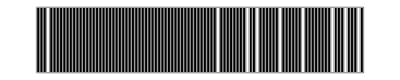
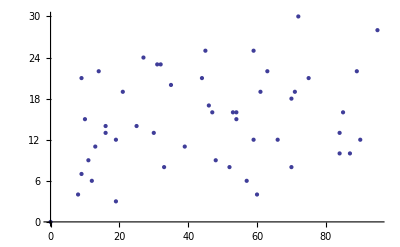
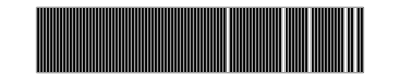
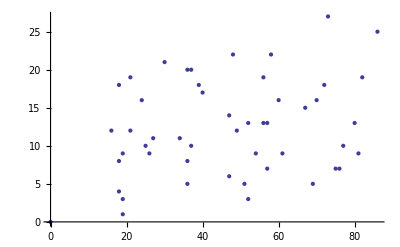
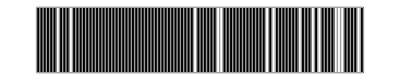
```mathematica
Export[fileName["genomePlot-75,1_10.pdf"],{{-Graphics--Graphics-, -Graphics--Graphics-, -Graphics--Graphics-, -Graphics--Graphics-, -Graphics--Graphics-, -Graphics--Graphics-, -Graphics--Graphics-, -Graphics--Graphics-, -Graphics--Graphics-, -Graphics--Graphics-}}]
```

/Users/caseygrun/codeshare/cs289/cs289-final-project/data_genomesize100_generations1000_mut0p01_cadist10/genomePlot-75,1_10.pdf

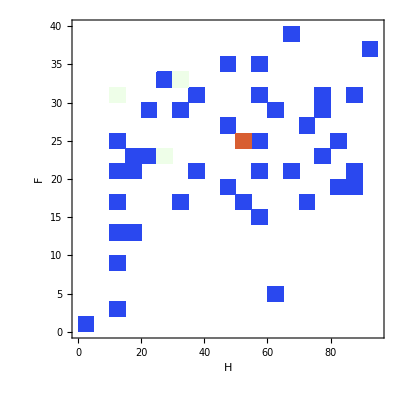
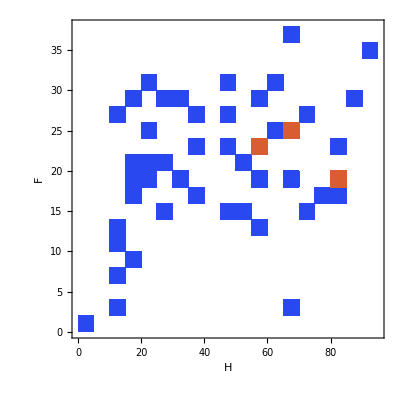
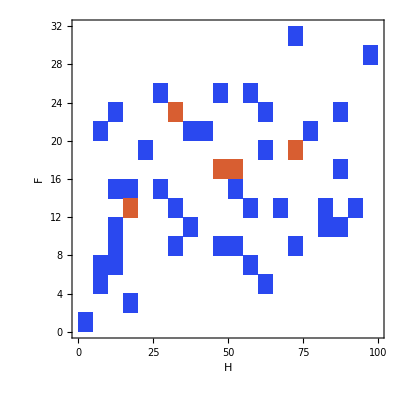
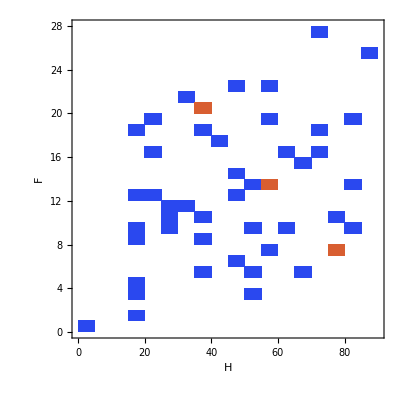
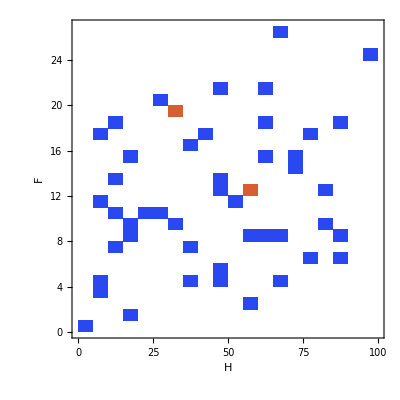
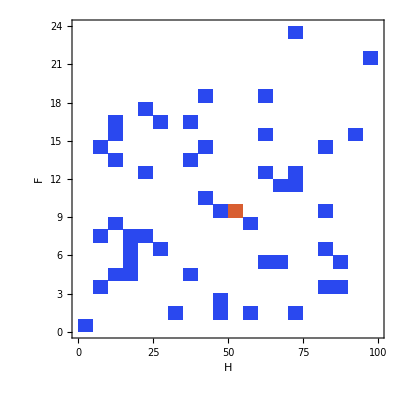
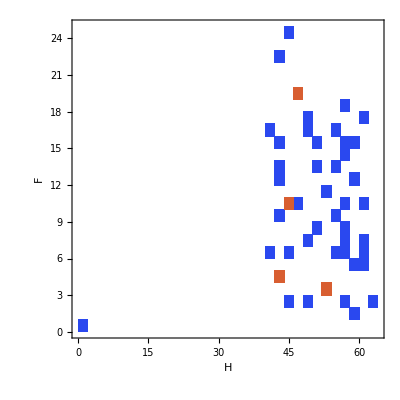
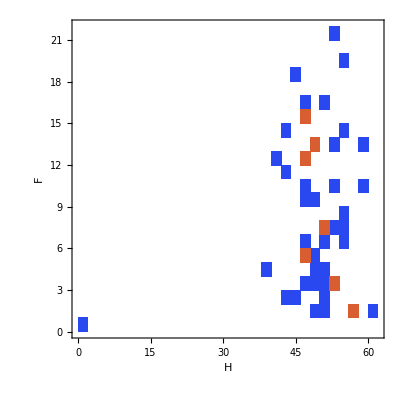
-Graphics-0.315075GenerationGenome-Graphics- | -Graphics-0.305592GenerationGenome-Graphics- | -Graphics-0.281455GenerationGenome-Graphics- | -Graphics-0.284941GenerationGenome-Graphics- | -Graphics-0.23332GenerationGenome-Graphics- | -Graphics-0.117774GenerationGenome-Graphics- | -Graphics-0.0295808GenerationGenome-Graphics- | -Graphics-0.130094GenerationGenome-Graphics- | -Graphics-0.0270028GenerationGenome-Graphics- | -Graphics-0.0717531GenerationGenome-Graphics-

```mathematica
Grid[Table[genomeHist2D[i,j],{i,75,75},{j,1,10}]]
```

```mathematica
findMaxes[mats_, k_]:=Module[{maxRows,maxCols},
maxRows= Ordering[mats,-k];
maxCols =Map[Ordering[#,-1][[1]]&,mats[[maxRows]]];
Transpose[{maxRows,maxCols}]
]
```

```mathematica
findMaxes[corrs,3]
```

{{76,40},{49,28},{27,46}}

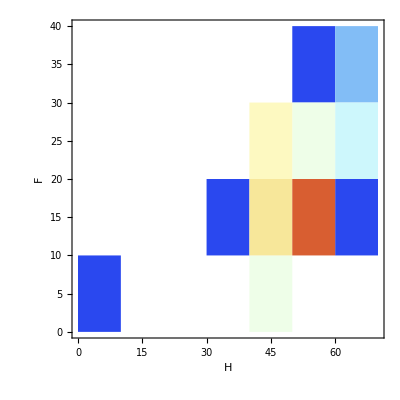
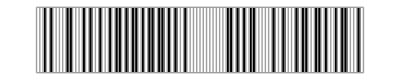
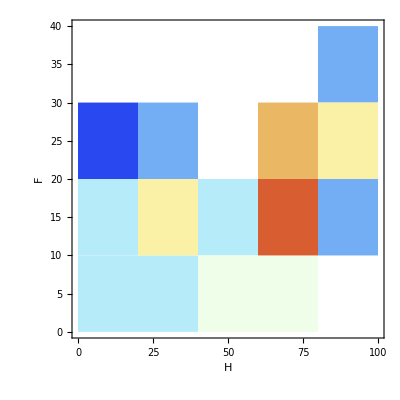
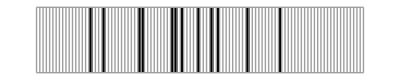
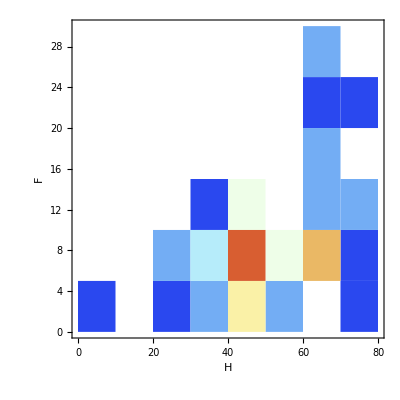
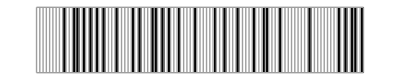
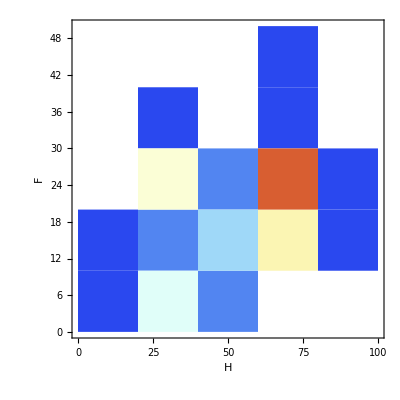
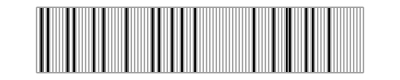
-Graphics-0.525039GenerationGenome-Graphics- | -Graphics-0.420034GenerationGenome-Graphics- | -Graphics-0.477507GenerationGenome-Graphics- | -Graphics-0.45672GenerationGenome-Graphics- | -Graphics-0.477934GenerationGenome-Graphics-

```mathematica
Grid[{Map[genomeHist2D@@#&,findMaxes[corrs,5]]}]
```

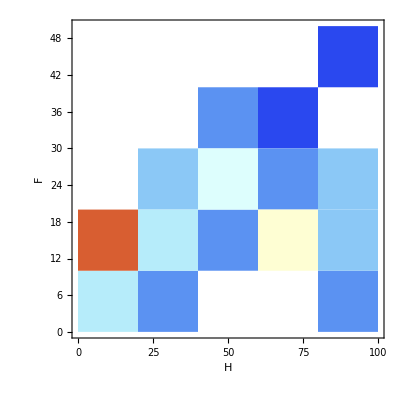
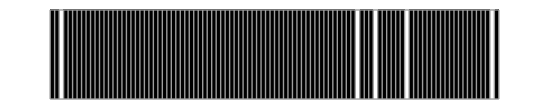
-Graphics-0.435326GenerationGenome-Graphics-

```mathematica
genomeHist2D[27,1]
```

```mathematica
?Min
```

Min[x_1,x_2,…] yields the numerically smallest of the x_i. 
Min[{x_1,x_2,…},{y_1,…},…] yields the smallest element of any of the lists.

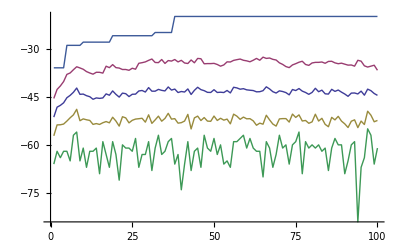

```mathematica
mns =Table[Mean[importFitnesses[j]],{j,1,100}];
stds = Table[StandardDeviation[importFitnesses[j]],{j,1,100}];
mins = Table[Min@@importFitnesses[j],{j,1,100}];
maxs = Table[Max@@importFitnesses[j],{j,1,100}];
ListLinePlot[{mns,mns+stds, mns-stds}]
```

```mathematica
Min@@importFitnesses[1]
```

-66

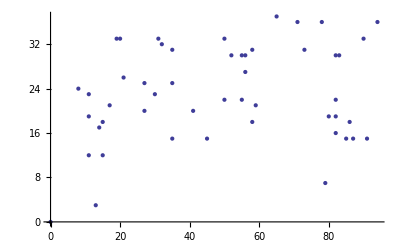
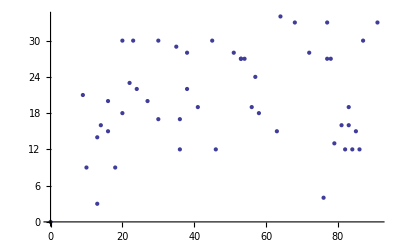
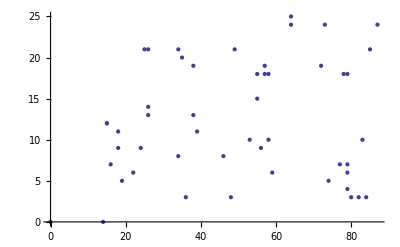
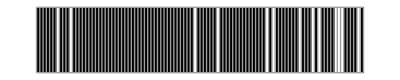
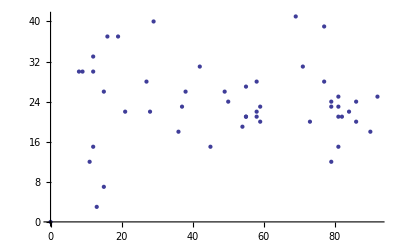
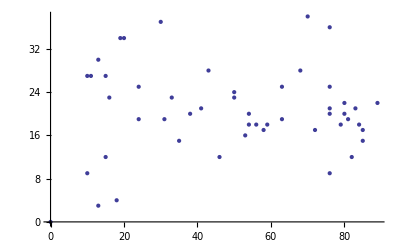
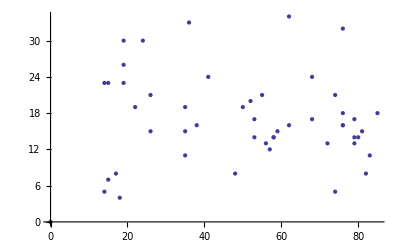
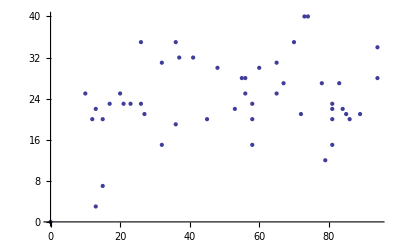
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Grid[Table[genomePlot[i,j],{i,70,80},{j,1,3}]]
```

```mathematica
allFits=Table[importFitnesses[j],{j,1,1000}];
```

```mathematica
findMaxes[allFits,4]
```

{{68,1},{69,1},{58,1},{59,1}}

```mathematica
Map[allFits[[#[[1]]]][[#[[2]]]]&,findMaxes[allFits,4]]
```

{-20,-20,-20,-20}

```mathematica
kFittestGenomes[k_]:=Map[importGenotype@@#&,findMaxes[allFits,k]];
kFittestGenomesAtGen[i_,k_]:=Map[importGenotype@@#&,findMaxesFlat[allFits,i,k]]
```

```mathematica
kFittestPhenos[k_]:=Map[importPhenotype@@#&,findMaxes[allFits,k]];
kFittestPhenosAtGen[i_,k_]:=Map[importPhenotype@@#&,findMaxesFlat[allFits,i,k]]
```

```mathematica
kFittestAtGen[i_,k_]:=Map[importFitness@@#&,findMaxesFlat[allFits,i,k]]
```

```mathematica
kFittestGenomes[5]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1}}

```mathematica
findMaxesFlat[allFits,1000,5]
```

{{1000,6},{1000,5},{1000,31},{1000,2},{1000,1}}

```mathematica
kFittestGenomesAtGen[1000,5]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,0,0,1,1,1,1,0,0,0,1,0,1,1,0,1,1,1,1,0,0,1,0,1,1,0,0,0,1,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,0,1,1,0,0,0,0,1,0,0,1,0,1,1,1,0,1,1,1,0,0,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,1,1,0,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1},{0,1,0,1,1,0,1,1,0,1,1,1,1,1,0,1,1,1,0,0,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,0,1,1,0,1,0,1,1,0,1,1,0,1,1,1,0,1,1,1,0,1,0,0,0,1,0,0,1,1,1,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,0,0,1,1,1,1,0,1,0,1,0,1,0,0,0,1,1}}

```mathematica
findMaxesFlat[allFits,1000,10]
```

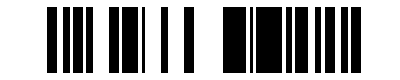
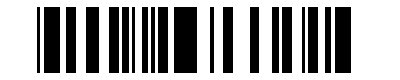
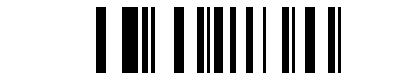
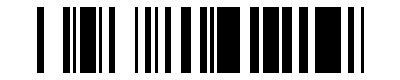
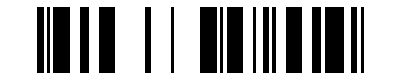
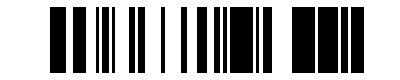
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ArrayPlot[{importPhenotype@@#}]&,{{1000,19},{1000,26},{1000,48},{1000,8},{1000,9},{1000,6},{1000,5},{1000,31},{1000,2},{1000,1}}]
```

```mathematica
Grid[Join[{{"Automaton","Genotype","Phenotype","Fitness"}},
Transpose[{
Map[ArrayPlot[CellularAutomaton[110,#[[2;;100]],10]]&,kFittestGenomesAtGen[1000,10]],
Map[ArrayPlot[{#}]&,kFittestGenomesAtGen[1000,10]],
Map[ArrayPlot[{#}]&,kFittestPhenosAtGen[1000,10]],
kFittestAtGen[1000,10]
}]
]]
```

Automaton | Genotype | Phenotype | Fitness
-Graphics- | -Graphics- | -Graphics- | -37
-Graphics- | -Graphics- | -Graphics- | -37
-Graphics- | -Graphics- | -Graphics- | -37
-Graphics- | -Graphics- | -Graphics- | -36
-Graphics- | -Graphics- | -Graphics- | -36
-Graphics- | -Graphics- | -Graphics- | -35
-Graphics- | -Graphics- | -Graphics- | -33
-Graphics- | -Graphics- | -Graphics- | -32
-Graphics- | -Graphics- | -Graphics- | -20
-Graphics- | -Graphics- | -Graphics- | -19

```mathematica
Export[fileName["different-genotype-similar-performance.pdf"],{{"Automaton", "Genotype", "Phenotype", "Fitness"}, {-Graphics-, -Graphics-, -Graphics-, -37}, {-Graphics-, -Graphics-, -Graphics-, -37}, {-Graphics-, -Graphics-, -Graphics-, -37}, {-Graphics-, -Graphics-, -Graphics-, -36}, {-Graphics-, -Graphics-, -Graphics-, -36}, {-Graphics-, -Graphics-, -Graphics-, -35}, {-Graphics-, -Graphics-, -Graphics-, -33}, {-Graphics-, -Graphics-, -Graphics-, -32}, {-Graphics-, -Graphics-, -Graphics-, -20}, {-Graphics-, -Graphics-, -Graphics-, -19}}]
```

/Users/caseygrun/codeshare/cs289/cs289-final-project/data_genomesize100_generations1000_mut0p01_cadist10/different-genotype-similar-performance.pdf

```mathematica
SystemOpen["/Users/caseygrun/codeshare/cs289/cs289-final-project/data_genomesize100_generations1000_mut0p01_cadist10/different-genotype-similar-performance.pdf"]
```

```mathematica
Map[StringJoin[Map[ToString,#]]&,kFittestGenomesAtGen[1000,10]]
```

```mathematica
{"0101101111110111111111111011101111111111011111111111101111111111110010111111111111111111011111101010","0101001100011000110101110110100101110001001001011011011100100001111110000111000111001010110100000011","0000000000000000000000100000000000000000100000000000000100010000000000000000000000000000000000000000","1111111011111111110001011111011110111010011110111111111111111110010111111111101111001111111111101111","0000000000001000000000000100110100000000000000010001000010000100000001000001000001010000010000001000","1111111111111111111111111111111111111011111111111111111111111111111111111111111111111011111111111111","0011100111100010110111100101100011100111010110010110000100101110111000111011111111110111111101101011","0000000000100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000","1111111111111111111111111111111111111111111111111111111111111111111111111111111111111111110111111111","0101101101111101110001000000111000010101101011011011101110100010011111100100001001100111101010100011"}
```